```mathematica
(*Mathematica*)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B]
```

```mathematica
sc=N[1];
```

```mathematica
s[1]=N[{{1+sc*I,sc},{sc,1-sc*I}}]
s[2]={{1.498960200807209,0.+0.09581565089154238 ⅈ},{0.+0.09581565089154238 ⅈ,0.6610044486242272}}
s[3]=Inverse[s[1]]
s[4]={{1.498960200807209,0.-0.09581565089154238 ⅈ},{0.-0.09581565089154238 ⅈ,0.6610044486242272}}
```

{{1.+1. ⅈ,1.},{1.,1.-1. ⅈ}}

{{1.49896,0.+0.0958157 ⅈ},{0.+0.0958157 ⅈ,0.661004}}

{{1.-1. ⅈ,-1.+0. ⅈ},{-1.+0. ⅈ,1.+1. ⅈ}}

{{1.49896,0.-0.0958157 ⅈ},{0.-0.0958157 ⅈ,0.661004}}

```mathematica
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
qf=N[rotate[Pi/4]];qfi=Inverse[qf]
```

{{0.707107,0.707107},{-0.707107,0.707107}}

```mathematica
{a,b,A,B}=Table[N[s0.qf.s[i].qfi.s1],{i,4}]
```

{{{1.+0. ⅈ,0.+0. ⅈ},{0.+2. ⅈ,1.+0. ⅈ}},{{1.07998+0. ⅈ,0.514794+0. ⅈ},{0.323162+0. ⅈ,1.07998+0. ⅈ}},{{1.+0. ⅈ,0.+0. ⅈ},{0.-2. ⅈ,1.+0. ⅈ}},{{1.07998+0. ⅈ,0.323162+0. ⅈ},{0.514794+0. ⅈ,1.07998+0. ⅈ}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

1.+0. ⅈ

2.+0. ⅈ

1.+0. ⅈ

2.15996+0. ⅈ

1.+0. ⅈ

2.+0. ⅈ

1.+0. ⅈ

2.15996+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],12];
ll=Length[aa1]
Last[aa1]
aa=aa1;
```

1594322

{1.26205,0}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->Hue,PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-.1,1.3},{-1.4/2,1.4/2}}];
```

```mathematica
Export["Nylander_3group_Shape_Matrix_PC35_extrapolated_scaleone_biquasiconformal45_Limitset12_g0.jpg",g0]
```

Nylander_3group_Shape_Matrix_PC35_extrapolated_scaleone_biquasiconformal45_Limitset12_g0.jpg

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[12*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

2

18

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-.1,1.3},{-1.4/2,1.4/2}},Background->Black];
```

```mathematica
Export["Nylander_3group_Shape_Matrix_PC35_extrapolated_scaleone_biquasiconformal45_Limitset12_g2.jpg",g2]
```

Nylander_3group_Shape_Matrix_PC35_extrapolated_scaleone_biquasiconformal45_Limitset12_g2.jpg

```mathematica
(* end limit set*)
```

```mathematica
(* Mathematica*)
```

```mathematica
Clear[x,y,a,b,f,z,g0,g1,g2,p,c,g]
g[z_]=(z^2+c);
```

```mathematica
nr=NestList[g,c,30];
```

```mathematica
v=Union[Flatten[ParallelTable[If[Abs[c]>=0.004965708144504987||Abs[c]≤2.0,c,Nothing]/.FindRoot[nr[[i]]==0,{c,x+I*y}][[1]],{x,-2.0,0.5,N[2.5/100+0.00001]},{y,-2.5/2,2.5/2,N[2.5/100+0.00001]},{i,30}]]];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
Dimensions[v]
```

{254503}

```mathematica
v1=Delete[Reverse[Union[v]],1];
```

```mathematica
gout=ComplexListPlot[v1,ColorFunction->"CMYKColors",ImageSize->2000,PlotStyle->PointSize[0.0025]];
```

```mathematica
Export["PC30_roots_pointsize0p0025.jpg",gout]
```

PC30_roots_pointsize0p0025.jpg

```mathematica
v1[[1]]
```

0.47599-0.34964 ⅈ

```mathematica
Clear[v]
```

```mathematica
v=ParallelTable[{Re[v1[[i]]],Im[v1[[i]]]},{i,Length[v1]}];
```

```mathematica
mv=Transpose[v].v//Chop
```

{{255488.,1866.92},{1866.92,103525.}}

```mathematica
m= mv/Sqrt[Det[mv]]//Chop
```

{{1.57105,0.0114801},{0.0114801,0.6366}}

```mathematica
(*PC25;{{1.6026450930791114,0.01120066064382996},{0.01120066064382996,0.6240467456692788}}*)
```

```mathematica
(*PC20:{{1.662865521770655,0.01063728869421},{0.01063728869421,0.6014395865552749}}*)
(*Pc10:{{1.750147012885839,0.005109430101885817},{0.005109430101885817,0.5713954878721936}}*)
(*PC14{{1.8676765820371843,0.00885505853021847},{0.00885505853021847,0.5354665907791858}}*)
(*PC7:{{3.5162233609325066,0.0011709396485965376},{0.0011709396485965376,0.2843964300477371}}*)
```

```mathematica
z1=Table[z/.Solve[Exp[z]==m[[i,j]],z]/.C[1]->0,{i,2},{j,2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{{0.451746},{-4.46714}},{{-4.46714},{-0.451614}}}

```mathematica
N[z1*180/Pi]
```

{{{25.8831},{-255.948}},{{-255.948},{-25.8756}}}

```mathematica
.10(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
w={(*{7,3.5162233609325066},*){10,1.750147012885839},{14,1.8676765820371843},{20,1.662865521770655},{25,1.6026450930791114},{30,1.5710530654318942}}
```

{{10,1.75015},{14,1.86768},{20,1.66287},{25,1.60265},{30,1.57105}}

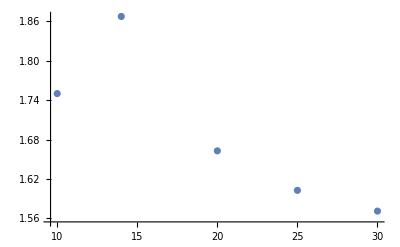

```mathematica
g1=ListPlot[w]
```

```mathematica
f[x_]=Fit[w,{1,x},x]
```

1.94087-0.0126261 x

```mathematica
f[35]
```

1.49896

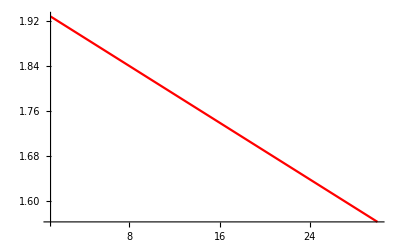

```mathematica
g2=Plot[f[x],{x,1,30},PlotStyle->Red]
```

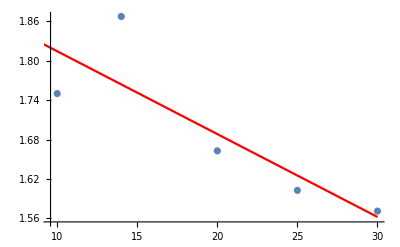

```mathematica
Show[{g1,g2}]
```

```mathematica
gr={{{3.5162233609325066,0.0011709396485965376},{0.0011709396485965376,0.2843964300477371}},{{1.750147012885839,0.005109430101885817},{0.005109430101885817,0.5713954878721936}},{{1.8676765820371843,0.00885505853021847},{0.00885505853021847,0.5354665907791858}},{{1.662865521770655,0.01063728869421},{0.01063728869421,0.6014395865552749}},{{1.6026450930791114,0.01120066064382996},{0.01120066064382996,0.6240467456692788}},{{1.5710530654318942,0.011480144443690587},{0.011480144443690587,0.6365996258958345}}}
```

{{{3.51622,0.00117094},{0.00117094,0.284396}},{{1.75015,0.00510943},{0.00510943,0.571395}},{{1.86768,0.00885506},{0.00885506,0.535467}},{{1.66287,0.0106373},{0.0106373,0.60144}},{{1.60265,0.0112007},{0.0112007,0.624047}},{{1.57105,0.0114801},{0.0114801,0.6366}}}

```mathematica
Apply[Plus,Table[Norm[gr[[i]].{1,1}],{i,Length[gr]}]]/6
```

2.09279

```mathematica
p={7,10,14,20,25,30}
```

{7,10,14,20,25,30}

```mathematica
g[x_]=Fit[Table[{p[[i]],Tr[gr[[i]]]},{i,2,Length[gr]}],{1,x},x]
```

2.44711-0.00820411 x

```mathematica
g[35]
```

2.15996

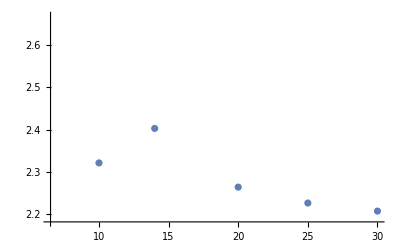

```mathematica
ListPlot[Table[{p[[i]],Tr[gr[[i]]]},{i,Length[gr]}]]
```

```mathematica
Table[{p[[i]],Tr[gr[[i]]]},{i,Length[gr]}]
```

{{7,3.80062},{10,2.32154},{14,2.40314},{20,2.26431},{25,2.22669},{30,2.20765}}

```mathematica
{{1.498960200807209,a0},{a0,2.159964649431436-1.498960200807209}}/.Solve[Det[{{1.498960200807209,a0},{a0,2.159964649431436-1.498960200807209}}]==1,a0]
```

{{{1.49896,0.-0.0958157 ⅈ},{0.-0.0958157 ⅈ,0.661004}},{{1.49896,0.+0.0958157 ⅈ},{0.+0.0958157 ⅈ,0.661004}}}

```mathematica
(*end*)
```